```mathematica
η=1*10^-2;
dt=0.1;
T=295;
dx=1.5625*10^-8
v=dx^3;
kb=1.3806*10^-16;
R=(1.176*10^-7);
```

1.5625×10^-8

```mathematica
χ=(kb T)/(6 π η R)
```

1.83731×10^-6

```mathematica
((2 χ)/dx^2)^-1
```

6.64398×10^-11

```mathematica
χ*1.01
```

0.0000134709

```mathematica
((1.6*10^-19)^2)/((8*10^-7)^2)
```

4.×10^-26

```mathematica
1/(8*10^-7)
```

1250000

```mathematica
dx=(25*10^-7)/64;
F=1;
V=(25*10^-7)^3;
U=142076186.21676001;

araw=Solve[F==6 π η a U (1.0+1.7601 ((4/3 π a^3)/V)^(1/3)),a][[1,1,2]];
araw/dx
```

0.91851

```mathematica
χ=(kb T)/(6 π η R)
```

0.0000133375

```mathematica
Solve[6 π η Rt == 6 π η Rw + 6 π η Rd,Rd]
```

{{Rd→Rt-Rw}}

```mathematica
Clear[srf]
eps =1*10^-16; σ=5*10^-8;q=4.8*10^-10;
srf[r_]=4 eps ((6 (σ/2)^6)/r^7-(12 (σ/2)^12)/r^13);
cf[r_]=-q^2/r^2;
```

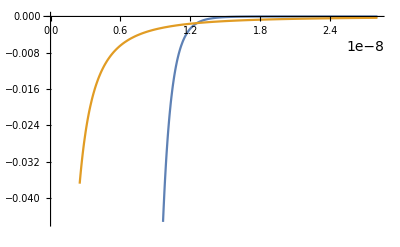

```mathematica
Plot[{srf[r],cf[r]},{r,0.1(σ/2),1.122(σ/2)},AxesOrigin->{0,0}]
```

```mathematica
dd=5.0*10^-8;
srf[dd]
cf[dd]/q
```

7.26563×10^-10

-192000.

```mathematica
DX=0.5*10^-5;
DY=DX;
DZ=DX;

litre=(10)^3;
TV=DX*DY*DZ;
molarity=0.001;

NN=(TV/litre)*6.02*10^23*molarity
```

75.25

```mathematica
6.02*10^23*molarity/litre
```

6.02×10^17

```mathematica
currentDensity=870000
eField=1.0 10^15;
currentDensity/eField
```

870000

8.7×10^-10

```mathematica
kbsi = 1.38*10^-23;
eosi =8.85*10^-12;
qsi=1.6*10^-19;
xsi = 10^-7;
xcgs = 6.25*10^-7;
eocgs = 692.96*10^-21;
qcgs = 1.6*10^-19;

Fsi=qsi^2/(eosi xsi^2 4 π);
Fcgs = qcgs^2/(eocgs xcgs^2 4 π)

Esi=qsi^2/(eosi xsi 4 π);
Ecgs = qcgs^2/(eocgs xcgs 4 π);
```

7.52596×10^-9

```mathematica
xcgs^2
```

3.90625×10^-13

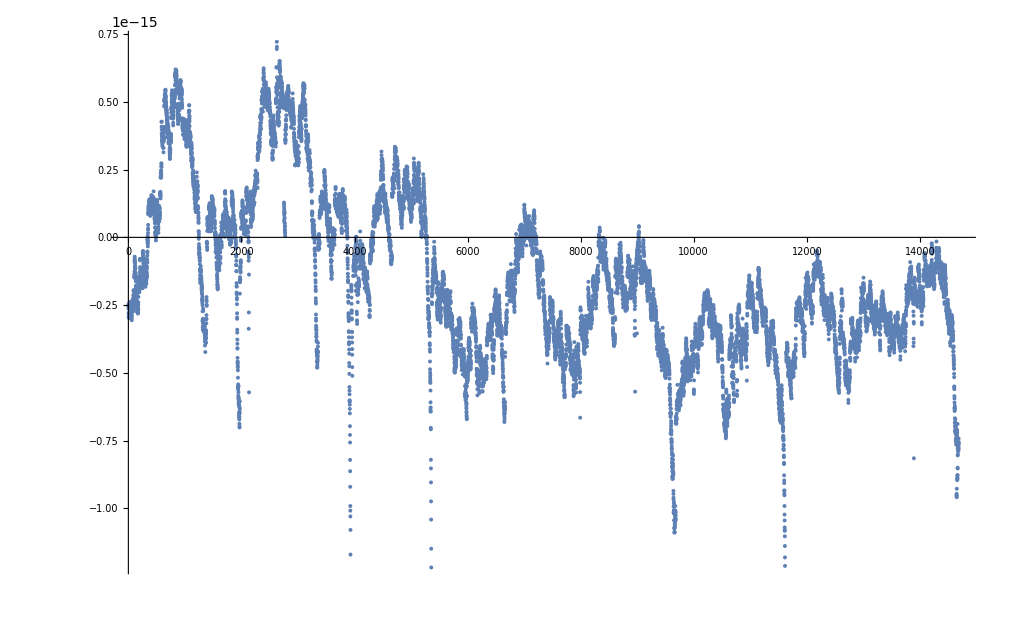

```mathematica
SetDirectory[NotebookDirectory[]];
potentialHistory=Flatten[Import["potential.dat","Table"]];
ListPlot[potentialHistory]
```

```mathematica
potentialHistory
```

{5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15,5.35072×10^-15}

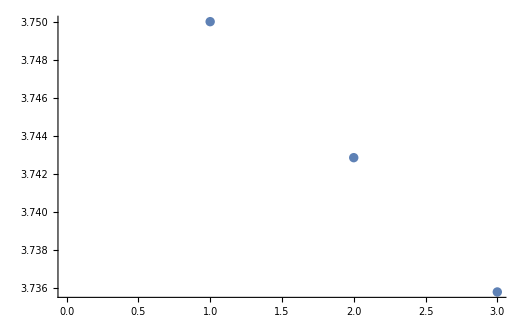

```mathematica
ListPlot[{3.75000,3.742846,3.7357816852}]
```

```mathematica
100^3
```

1000000

```mathematica
(((300.0*10^-8)^3)/(10^3))*6.02*10^23*0.1
```

1625.4

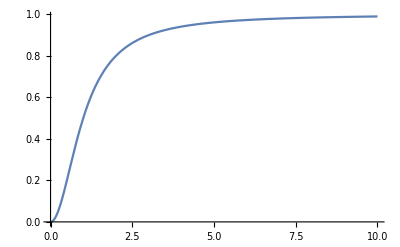

```mathematica
Plot[k^2/(1+k^2),{k,0,10},PlotRange->All]
```